```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=16;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=17;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f;
Jrf=σr1f+σr2f+σr3f+σr4f;
Jxf=Jlf+Jrf;
ρeegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];

ρgege0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgeeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggee0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];


(*设定参数*)
ωr=8*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;
Δ=0.4*ωr;
γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=200;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωr*adaigef.af+Δ*(ρggee0+ρgeeg0+ρgege0+ρegge0+ρegeg0+ρeegg0)+g*(adaigef.(σl1f)+af.(σr1f))+g*(adaigef.(σl2f)+af.(σr2f))+g*(adaigef.(σl3f)+af.(σr3f))+g*(adaigef.(σl4f)+af.(σr4f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,15,30,0.5}];
data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

```mathematica
{{15.,0.5325826737121373},{15.5,0.6588873414342359},{16.,0.6570596304236058},{16.5,0.5694922630609934},{17.,0.4252851337001244},{17.5,0.24482269743769924},{18.,0.04449086306998229},{18.5,-0.16987504929230626},{19.,-0.383376229552659},{19.5,-0.5722685379397023},{20.,-0.7000875228582308},{20.5,-0.7443218285902983},{21.,-0.718668243414049},{21.5,-0.6563714792918427},{22.,-0.5853695349121185},{22.5,-0.5167829547569409},{23.,-0.4584127993144388},{23.5,-0.40201970160174694},{24.,-0.3581887694722225},{24.5,-0.3214680374193466},{25.,-0.28475553642016804},{25.5,-0.2548494967574513},{26.,-0.23601491601111838},{26.5,-0.21457058565244663},{27.,-0.19305711531000846},{27.5,-0.17615030122847042},{28.,-0.16333584407127855},{28.5,-0.14994207230946732},{29.,-0.1405973614635291},{29.5,-0.13040448495998253},{30.,-0.11953738705885283}}
```

```mathematica
data={{15.,0.5325826737121373},{15.5,0.6588873414342359},{16.,0.6570596304236058},{16.5,0.5694922630609934},{17.,0.4252851337001244},{17.5,0.24482269743769924},{18.,0.04449086306998229},{18.5,-0.16987504929230626},{19.,-0.383376229552659},{19.5,-0.5722685379397023},{20.,-0.7000875228582308},{20.5,-0.7443218285902983},{21.,-0.718668243414049},{21.5,-0.6563714792918427},{22.,-0.5853695349121185},{22.5,-0.5167829547569409},{23.,-0.4584127993144388},{23.5,-0.40201970160174694},{24.,-0.3581887694722225},{24.5,-0.3214680374193466},{25.,-0.28475553642016804},{25.5,-0.2548494967574513},{26.,-0.23601491601111838},{26.5,-0.21457058565244663},{27.,-0.19305711531000846},{27.5,-0.17615030122847042},{28.,-0.16333584407127855},{28.5,-0.14994207230946732},{29.,-0.1405973614635291},{29.5,-0.13040448495998253},{30.,-0.11953738705885283}};

ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Red},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

-Graphics-

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

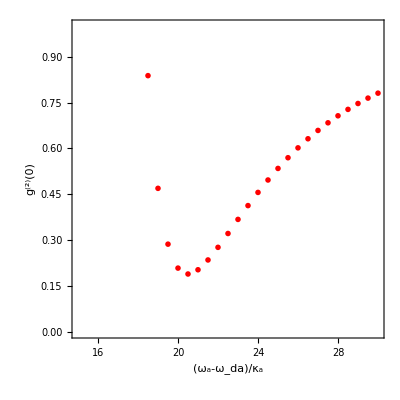

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=4;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Red},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

```mathematica
data={{15.,0.9935289188565168},{15.5,0.6863379030840118},{16.,0.37058293035532613},{16.5,0.45936234011912136},{17.,0.6724069255335803},{17.5,0.7549210206477538},{18.,0.7260068096456006},{18.5,0.6227110951114133},{19.,0.47523936030031244},{19.5,0.30193498331097124},{20.,0.10644777509359445},{20.5,-0.10258378174749742},{21.,-0.3157141973692337},{21.5,-0.5226017864888515},{22.,-0.6928584457700621},{22.5,-0.7925048241939511},{23.,-0.8081422032709489},{23.5,-0.7643042425801835},{24.,-0.6923210940809711},{24.5,-0.6197937246065547},{25.,-0.5471708196423297},{25.5,-0.48893299680638863},{26.,-0.43351546003284497},{26.5,-0.3865717453632773},{27.,-0.3474171453713389},{27.5,-0.31364756775346964},{28.,-0.2803985426339257},{28.5,-0.2592792749934748},{29.,-0.23878540736018372},{29.5,-0.21857099678111608},{30.,-0.19886265990635918}};

ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Green},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

-Graphics-

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

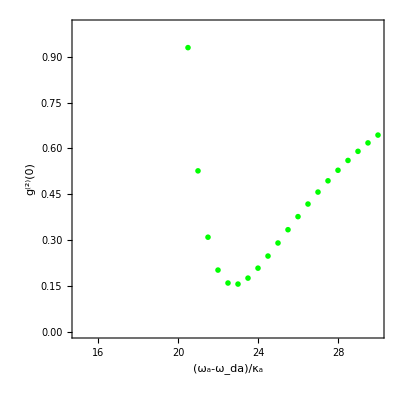

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=5;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Green},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

```mathematica
data={{15.,1.4603804729365528},{15.5,1.3856855629927318},{16.,1.2763637984219598},{16.5,1.1050606859959324},{17.,0.8318874513590846},{17.5,0.4812317697886755},{18.,0.448744904542083},{18.5,0.6863614161949961},{19.,0.8129574020129737},{19.5,0.8173967203668225},{20.,0.7390010887099002},{20.5,0.610642937672666},{21.,0.45462785801514527},{21.5,0.27823609905270397},{22.,0.08293529990022898},{22.5,-0.12100976728753639},{23.,-0.33200960536744595},{23.5,-0.5391577021500099},{24.,-0.7187983613258617},{24.5,-0.8355022814767307},{25.,-0.867996769437574},{25.5,-0.8323407798531478},{26.,-0.7612022397450943},{26.5,-0.6835560262983051},{27.,-0.6077026754673762},{27.5,-0.5441404102186848},{28.,-0.48466198888734446},{28.5,-0.43514690688775653},{29.,-0.39487375157292853},{29.5,-0.35466371024163645},{30.,-0.31998392413771776}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Orange},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

-Graphics-

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

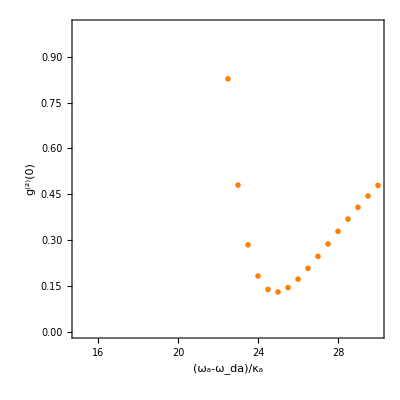

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=6;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Orange},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

```mathematica
data={{15.,1.626991843654391},{15.5,1.588162741740107},{16.,1.5504297664852507},{16.5,1.485352328417293},{17.,1.4184897328075536},{17.5,1.3164420806935642},{18.,1.1469501982577632},{18.5,0.8781633884306504},{19.,0.5301876893062966},{19.5,0.49368993789664967},{20.,0.7350229943741762},{20.5,0.8678537475282341},{21.,0.8783444420685225},{21.5,0.8122410807351802},{22.,0.6952704121454186},{22.5,0.5445840381863504},{23.,0.3765066561126365},{23.5,0.19641195810874235},{24.,0.0004974066663070995},{24.5,-0.2032188918072156},{25.,-0.41109090396123144},{25.5,-0.6143776230687087},{26.,-0.786482567014444},{26.5,-0.8926093074575614},{27.,-0.9154483671595929},{27.5,-0.8728975367908842},{28.,-0.7977306929908327},{28.5,-0.7184302985869492},{29.,-0.6401963911726203},{29.5,-0.575825701232004},{30.,-0.5149549065420309}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Blue},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

-Graphics-

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

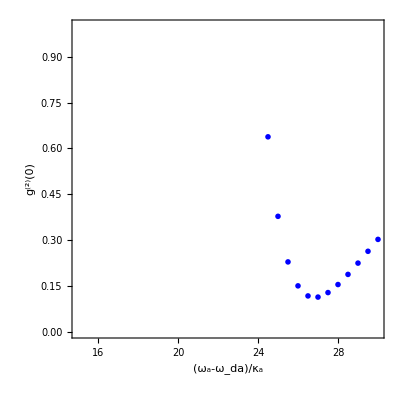

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=7;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)

ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_a-ω_da)/κ_a","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Blue},Frame->True,PlotRange->{{15,30},{0,1}},AspectRatio->1]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-